```mathematica
<<IGraphM`
```

IGraph/M 0.3.97.2 (February 5, 2018)

Evaluate IGDocumentation[] to get started.

```mathematica
Clear[latticer]

latticer[n_, r_]:=
(* Created a 1D periodic lattice with radius r *)
IGMakeLattice[{n},Radius ->r,Periodic->True]
```

```mathematica
Clear[setVertexProp]

setVertexProp[g_,prop_,vals_]:=
(*
	Sets the property prop of the vertices in g to vals;

	input;
		g: graph;
		prop: property of vertex;
		vals: a list of values;

	output;
		a graph
*)
Module[
{h=g,vl=VertexList@g},
Do[
PropertyValue[
{
h,
vl[[i]]
},
prop
]=vals[[i]],
{i,Length@vl}
];
Return@h]
```

```mathematica
Clear[grapherSi]

grapherSi[n_, k_, e_,si_] :=
(*
	Creates a graph of n members with random states (0/1);
	linked to their k nearest neighbors;
	The links are then each rewired with probability e;

	input;
		n: number of members;
		k: degrees of vertex;
		e: probablity of rewiring;

	outputs;
		a graph
*)

Module[
{r, states, graph,g1},

r = (* radius of lattice *)
Round[k/2];

states = (* a list of random states between 0 <-> 1 *)
RandomSample[
Join[
Table[0, si],
Table[1, n-si]]];

graph=  

setVertexProp[ (* sets the "State"s and VertexLabels to 'states' *)

IGRewireEdges[ (* rewires the graph with probability e *)
latticer[n,r],(* creates a graph of n members with radius r *)
e
],  

{"State", VertexLabels}, 
states

]
]
```

```mathematica
Clear[stringer]

(* creates a value "abi" for dummy variables in majority *)
stringer[i_] := "ab"<>ToString[i]
```

```mathematica
Clear[majority]

majority[h_, list_] :=
True /; (Length[list ] == 2) ∧ (list[[1]] == list[[2]])

majority[h_, list_] :=
False /; (Length[list] == 2) ∧ !(list[[1]] == list[[2]])

majority[ h_, list_]:= 
(*
	Returns True if a majority above the threshold 'h' is reached in list;
	Returns False if no majority above the threshold 'h' is reached in list;

	inputs;
		h:    threshold;
		list: list of elements to check;

	outputs;
		True or False;
*)
Module[
{
ab, swaps
},

ab = Table[stringer[i], {i, 1, Length[list]}];  (* dummy list of {ab1, ab2, ab3, ..., abN} where N is the length of list *)
swaps =  Dispatch[Table[ab[[i]] -> list[[i]], {i, 1, Length[list]}]]; (* creates a list of transformations {ab1 -> list[1], ab2 -> list[2], ..., abN -> list[N]} to swap back after BooleanCountingFunction *)

BooleanConvert[
(* converts from a functional form to disjunctive normal form *)
BooleanCountingFunction[
(* compares elements in list (element1 ∧ element2, ∧ is later swapped with ==) and returns True if at least a majority above the threshold h are agree  *)
{
Ceiling[h Length[list]],
Length[list]
},
Length[list]
] @@ ab

] //. swaps //. And -> Equal
]
```

```mathematica
Clear[newState]

(*
	Returns the new state of a vertex;

	inputs;
		v:    current state of vertex;
		h:    threshold;
		list: list of elements to check;

	outputs;
		1 or 0;

*)
newState[v_,h_, list_] :=
0 /;( majority[h,list] ∧ (Commonest[list][[1]] == 0))

newState[v_,h_,list_] :=
1 /; (majority[h, list] ∧ (Commonest[list][[1]] == 1))

newState[v_, h_, list_] := 
v /; !majority[h, list]

newState[v_,h_,list_] := 
list[[1]] /; Length[list] == 1
```

```mathematica
Clear[associatedAdjacencyLister]

associatedAdjacencyLister[g_] :=
(* 
Creates an association of vertices with vertices they are connected to;
(ie if vertex 1 is connected to {2,3,4} it would return <|1 -> {2,3,4},...|>);
*)
AssociationThread[
Range[1, Length[VertexList[g]]],
AdjacencyList[g,#] & /@ VertexList[g]
]
```

```mathematica
Clear[seter]

SetAttributes[seter, HoldFirst];

seter[g_,key_,value_,h_] :=
(*
	Sets the state of a vertex, key, with a value depending on value;

	inputs;
		g:     graph;
		key:   vertex to be updated;
		value: neighboring vertices;
		h:     threshold;

	outputs;
		nothing;
*)
Module[
{
s, properties
},

s = PropertyValue[{g, key},"State"];
properties = PropertyValue[{g, #}, "State"] &/@ value;

PropertyValue[{g,key}, "State"] = newState[s, h, properties]]
```

```mathematica
Clear[propertyChanger]

SetAttributes[propertyChanger, HoldFirst];

propertyChanger[graph_, l_, h_] :=
(*
	Threads through the associated adjacency list l, updating the states of the vertices using seter;

	inputs;
		graph: graph;
		l:     associated adjacency list;
		h:     threshold;

	outputs;
		nothing;
*)
MapThread[
seter[graph,#1,#2,0.6] &,{Keys[l], Values[l]}]
```

```mathematica
Clear[iterator]

SetAttributes[iterator, HoldFirst];

iterator[g_, h_] := 
(*
	Creates an associated adjacency list with a random order, then changes the states of the vertices using propertyChanger;

	inputs;
		g: graph;
		h: threshold;

	outputs;
		nothing;
*)
Module[
{propertyList},
propertyList =RandomSample[associatedAdjacencyLister[g]];

propertyChanger[g, propertyList, h]
]
```

```mathematica
Clear[modelerSi]

modelerSi[n_, {k_, h_, e_}, i_, si_] := 
(* 
	Implementation of Parkinson's Law  for decision-making in committees;
	

	inputs;
		n: committee size (n ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

		i: iterations;


	outputs;
		a list of states, and the final graph;
*)

Module[
{graph,o,states, plot},
graph = grapherSi[n, k, e,si];
states = {Table[PropertyValue[{graph, o}, "State"], {o, 1, n}]};


Do[
iterator[graph,h]; 
AppendTo[states, Table[PropertyValue[{graph, o}, "State"], {o, 1, n}]], 
i
];

plot = ArrayPlot[states, Mesh->True];

{states, graph}
]
```

```mathematica
Clear[finalState]

(* Extracts the final states of the vertices from the output of modelerSi *)
finalState[m_] := m[[1]][[-1]]
```

```mathematica
Clear[plotter]

plotter[m_] :=  (* Plots an array of the evolution of states *)
ArrayPlot[m[[1]], Mesh-> True]
```

```mathematica
Clear[grapher]

(* displays the graph from the output of modelerSi *)
grapher[m_] :=m[[2]]
```

```mathematica
Clear[d]


(*
	Heaviside function that returns 0 if all the vertices agree and 1 if any disagree;

	inputs;
		n:  number of members;
		sf: number of members with final state 0;

	outputs;
		1 or 0;
*)
d[n_, sf_] := 0 /; (n == sf)  ∨ (sf == 0)
d[n_, sf_] := 1 /; n ≠ sf
```

```mathematica
Clear[dissensus]

dissensus[n_, {k_, h_, e_}, i_]:=
(*
	Gives the expectation value of a final state without consensus and measures the groups proneness to end up in dispute;

	Subscript[⟨θ(1 - (max(Subscript[S, f], N - Subscript[S, f]))/N)⟩, Subscript[S, i]];
	
	where;
		θ(x):  d[n, sf];
		Subscript[S, f]:    number of members with final state 0;
		Subscript[S, i]:    number of members with inital state 0;
		N:     number of members;


	inputs;
		n: committee size (n ∈ ℕ);

		{k, h, e}: model parameters;
			k: connectivity (number of undirected links between nodes) (k ∈ ℕ);
			h: threshold (h ∈ [0.5, 1]);
			e: rewiring probability (e ∈ [0, 1]);

		i: iterations;

	outputs;
		a ∈ [0, 1]
*)
Module[
{ms,fs,ds},
ms = Table[modelerSi[n, {k, h, e}, i, si], {si, 0, n}];

fs = finalState /@ ms;

ds = d[n, Count[#, 0]] & /@ fs;

Mean[ds]
]
```

```mathematica
tt = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {8, 0.6,0.1}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

{2246.6,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/9},{9,0},{10,0},{11,0},{12,1/65},{13,1/70},{14,2/75},{15,1/32},{16,7/170},{17,7/180},{18,6/95},{19,3/50},{20,2/21},{21,9/110},{22,19/230},{23,3/40},{24,14/125},{25,8/65},{26,41/270},{27,9/70},{28,9/58},{29,47/300},{30,11/62},{31,23/160},{32,17/110},{33,23/170},{34,53/350},{35,7/45},{36,13/74},{37,4/19},{38,79/390},{39,37/200},{40,42/205}}}

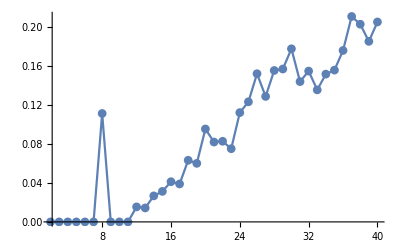

```mathematica
ListPlot[tt[[2]], Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic]
```

```mathematica
ll[[2]]
```

{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/90},{9,7/100},{10,3/110},{11,7/120},{12,3/65},{13,2/35},{14,1/15},{15,1/8},{16,21/170},{17,5/36},{18,13/95},{19,3/20},{20,19/105},{21,19/110},{22,41/230},{23,7/30},{24,24/125},{25,1/5},{26,7/30},{27,11/56},{28,38/145},{29,1/4},{30,36/155},{31,87/320},{32,13/55},{33,43/170},{34,101/350},{35,19/72},{36,99/370},{37,103/380},{38,10/39},{39,5/16},{40,66/205}}

```mathematica
ll =  
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.6,0.1}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

{947.505,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/90},{9,7/100},{10,3/110},{11,7/120},{12,3/65},{13,2/35},{14,1/15},{15,1/8},{16,21/170},{17,5/36},{18,13/95},{19,3/20},{20,19/105},{21,19/110},{22,41/230},{23,7/30},{24,24/125},{25,1/5},{26,7/30},{27,11/56},{28,38/145},{29,1/4},{30,36/155},{31,87/320},{32,13/55},{33,43/170},{34,101/350},{35,19/72},{36,99/370},{37,103/380},{38,10/39},{39,5/16},{40,66/205}}}

```mathematica
bb = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.6,0.05}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

{1120.12,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,1/30},{9,3/100},{10,4/55},{11,1/15},{12,6/65},{13,19/140},{14,8/75},{15,5/32},{16,1/5},{17,19/90},{18,17/95},{19,9/50},{20,8/35},{21,5/22},{22,51/230},{23,47/240},{24,69/250},{25,67/260},{26,13/45},{27,69/280},{28,9/29},{29,41/150},{30,87/310},{31,49/160},{32,103/330},{33,101/340},{34,113/350},{35,23/72},{36,123/370},{37,123/380},{38,1/3},{39,9/25},{40,14/41}}}

```mathematica
cc = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {6, 0.8, 0.1}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

{1090.56,{{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,1/20},{10,1/110},{11,1/20},{12,6/65},{13,1/10},{14,1/15},{15,21/160},{16,12/85},{17,1/10},{18,27/190},{19,3/20},{20,2/15},{21,31/220},{22,9/46},{23,3/16},{24,24/125},{25,9/52},{26,28/135},{27,3/14},{28,59/290},{29,71/300},{30,7/31},{31,43/160},{32,27/110},{33,24/85},{34,99/350},{35,23/90},{36,93/370},{37,3/10},{38,107/390},{39,7/25},{40,129/410}}}

```mathematica
dd = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {4, 0.8, 0.1}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{745.798,{{2,0},{3,0},{4,0},{5,0},{6,1/35},{7,3/80},{8,1/9},{9,2/25},{10,8/55},{11,1/6},{12,19/130},{13,6/35},{14,16/75},{15,9/40},{16,21/85},{17,7/30},{18,53/190},{19,57/200},{20,3/10},{21,3/10},{22,38/115},{23,77/240},{24,3/10},{25,47/130},{26,49/135},{27,97/280},{28,103/290},{29,107/300},{30,12/31},{31,23/64},{32,43/110},{33,139/340},{34,2/5},{35,19/45},{36,81/185},{37,157/380},{38,11/26},{39,93/200},{40,189/410}}}

```mathematica
ee = 
Partition[
Riffle[
Range[2,40],
Table[
Mean[
Table[
dissensus[n, {4, 0.6, 0.1}, 4], 10
]],
{n, 2, 40}
]],2] // AbsoluteTiming
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{745.658,{{2,0},{3,0},{4,0},{5,0},{6,1/70},{7,3/80},{8,1/18},{9,2/25},{10,1/11},{11,1/6},{12,19/130},{13,3/14},{14,1/5},{15,21/80},{16,19/85},{17,53/180},{18,26/95},{19,7/25},{20,17/70},{21,59/220},{22,42/115},{23,5/16},{24,46/125},{25,17/52},{26,47/135},{27,51/140},{28,107/290},{29,23/60},{30,59/155},{31,63/160},{32,13/33},{33,69/170},{34,143/350},{35,5/12},{36,77/185},{37,33/76},{38,53/130},{39,181/400},{40,88/205}}}

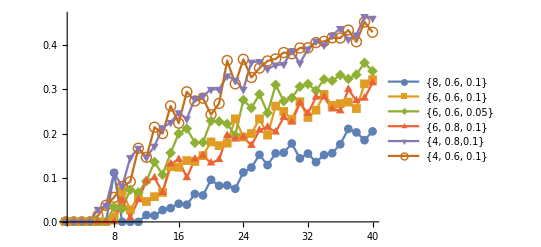

```mathematica
ListPlot[{tt[[2]],ll[[2]], bb[[2]], cc[[2]], dd[[2]], ee[[2]]}, Joined->True, PlotRange->{{2, 40}, Full}, PlotMarkers->Automatic, PlotLegends->{"{8, 0.6, 0.1}", "{6, 0.6, 0.1}", "{6, 0.6, 0.05}", "{6, 0.8, 0.1}", "{4, 0.8,0.1}", "{4, 0.6, 0.1}"}]
```

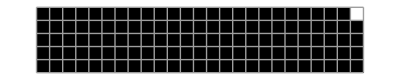
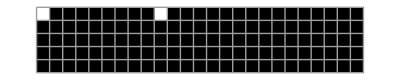
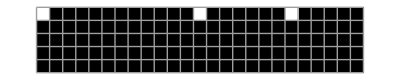
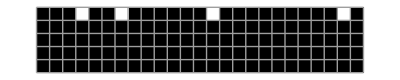
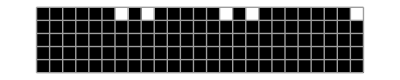
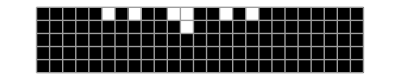
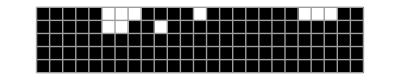
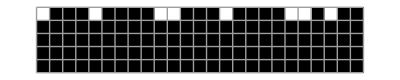

```mathematica
Table[plotter[modelerSi[25, {8, 0.8, 0.1}, 4,n]], {n, 1, 15}]
```